```mathematica
epsilon = 0.01;sheet = MeshRegion[{{0,0},{0,1},{1,0},{1,1}},{Triangle[{1,2,3}],Triangle[{2,3,4}]}];rod = MeshRegion[{{1,0.5-epsilon},{1,0.5+epsilon},{2,0.5-epsilon},{2,0.5+epsilon}},{Triangle[{1,2,3}],Triangle[{2,3,4}]}];
reg = RegionUnion[sheet,rod];
```

```mathematica
kk = 50;
initFunc[x_,y_]:=kk*x^2*(x-2)^2*y^2*(y-1)^2;
```

```mathematica
(*Whole region, alphaSheet for all diffusion*)
alphaSheet  = 0.02; alphaRod=0.8;
diffFunc[x_]:=Piecewise[{{alphaSheet,x<1},{alphaRod,x>1}}];
valsUniformDiffusion = NDSolveValue[{D[u[t,x,y],t]==alphaSheet*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
valsNonUniformDiffusion = NDSolveValue[{D[u[t,x,y],t]==diffFunc[x]*Laplacian[u[t,x,y],{x,y}],u[0,x,y]==initFunc[x,y]},u,{t,0,10},{x,y}∈reg];
Manipulate[Plot3D[{valsUniformDiffusion[t,x,y],
valsNonUniformDiffusion[t,x,y],
0,3},{x,y}∈reg,
PlotLegends->{"Uniform Diffusion","Higher Diffusion in Rod"}],{t,0,10}]
```

```mathematica
yy=0.5;Manipulate[Plot[{valsUniformDiffusion[t,x,yy],valsNonUniformDiffusion[t,x,yy],0,3},{x,0,2},PlotLegends->{"Uniform Diffusion","Higher Diffusion in Rod"}],{t,0,10}]
```

```mathematica
XderivUniformDiffusion[t_,x_,y_]:=D[valsUniformDiffusion[tV,xV,yV],xV]/.{tV->t,xV->x,yV->y};
XderivNonUniformDiffusion[t_,x_,y_]:=D[valsNonUniformDiffusion[tV,xV,yV],xV]/.{tV->t,xV->x,yV->y};
```

```mathematica
YderivUniformDiffusion[t_,x_,y_]:=D[valsUniformDiffusion[tV,xV,yV],yV]/.{tV->t,xV->x,yV->y};
YderivNonUniformDiffusion[t_,x_,y_]:=D[valsNonUniformDiffusion[tV,xV,yV],yV]/.{tV->t,xV->x,yV->y};
```

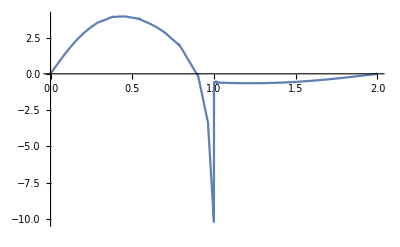

```mathematica
(*Diffusion in middle of system*)
tVV=0.4;
Plot[XderivNonUniformDiffusion[tVV,x,0.5],{x,0,2}]
```

```mathematica
(*Y diffusion in middles*)
```

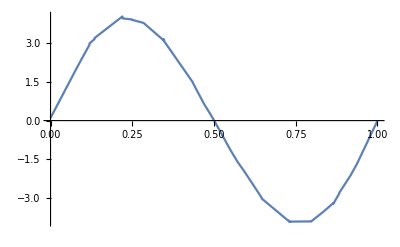

```mathematica
Plot[YderivNonUniformDiffusion[tVV,0.5,y],{y,0,1}]
```

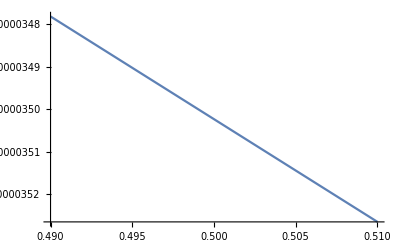

```mathematica
Plot[YderivNonUniformDiffusion[tVV,1.5,y],{y,0.5-epsilon,0.5+epsilon}]
```

```mathematica
(*
tVV = 5;
Plot[YderivNonUniformDiffusion[tVV,x,0.5+epsilon],{x,0,2}]
Plot[YderivNonUniformDiffusion[tVV,x,0.5-epsilon],{x,0,2}]
Plot[YderivNonUniformDiffusion[tVV,x,0],{x,0,2}]
Plot[YderivNonUniformDiffusion[tVV,x,1],{x,0,2}]
Plot[XderivNonUniformDiffusion[tVV,0,y],{y,0,1}]
Plot[XderivNonUniformDiffusion[tVV,1,y],{y,0,1}]
Plot[XderivNonUniformDiffusion[tVV,2,y],{y,0,1}]
*)
```

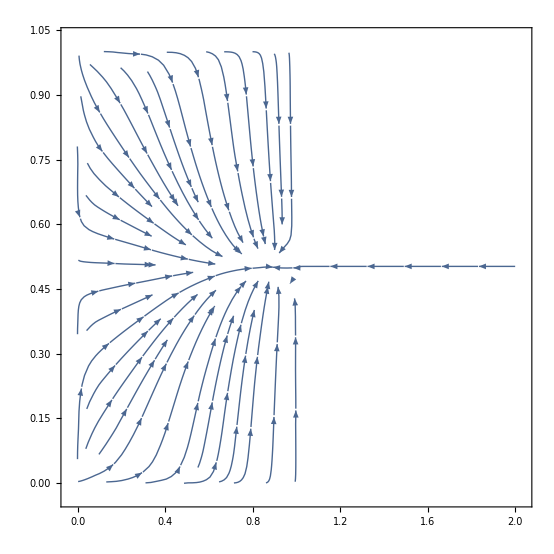

```mathematica
(*Initial Stream Plot*)
t0=0.5;StreamPlot[{XderivNonUniformDiffusion[t0,x,y],YderivNonUniformDiffusion[t0,x,y]},{x,y}∈reg]
```

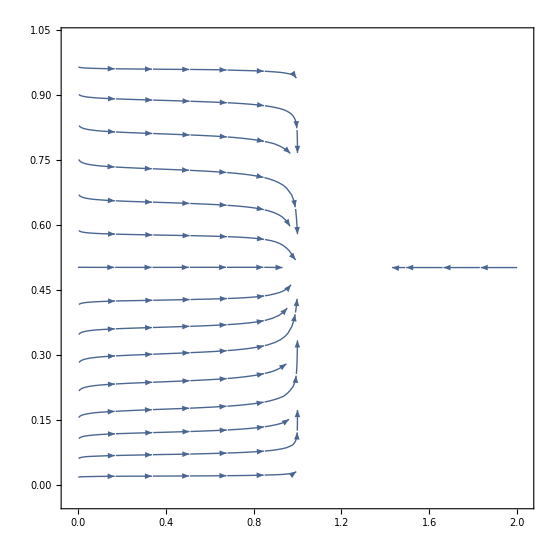

```mathematica
(*Later stream plot*)
t0=8;StreamPlot[{XderivUniformDiffusion[t0,x,y],YderivUniformDiffusion[t0,x,y]},{x,y}∈reg]
```

```mathematica
Table[NIntegrate[valsNonUniformDiffusion[curT,x,y],{x,y}∈reg],{curT,0.1,9.1,1}]
```

{0.92222,0.92222,0.92222,0.92222,0.92222,0.92222,0.92222,0.92222,0.92222,0.92222}